## Task 4 _ 1

## Variant 3

```mathematica
stE = DSolve[{y''[t]+0.2*y'[t]+y[t]== Sin[t], y[0] == 1, y'[0] == 0}, y[t], {t, 0, 4*π}]
```

{{y[t]→Sin[0.994987 t] (0.603023 ⅇ^(-0.1 t)-0.251259 Cos[0.00501256 t]-0.251259 Cos[1.99499 t]+5.01259 Sin[0.00501256 t]+0.0125945 Sin[1.99499 t])+Cos[0.994987 t] (6. ⅇ^(-0.1 t)-5.01259 Cos[0.00501256 t]+0.0125945 Cos[1.99499 t]-0.251259 Sin[0.00501256 t]+0.251259 Sin[1.99499 t])}}

```mathematica
stE⟦1, 1⟧
```

y[t]→Sin[0.994987 t] (0.603023 ⅇ^(-0.1 t)-0.251259 Cos[0.00501256 t]-0.251259 Cos[1.99499 t]+5.01259 Sin[0.00501256 t]+0.0125945 Sin[1.99499 t])+Cos[0.994987 t] (6. ⅇ^(-0.1 t)-5.01259 Cos[0.00501256 t]+0.0125945 Cos[1.99499 t]-0.251259 Sin[0.00501256 t]+0.251259 Sin[1.99499 t])

```mathematica
Evaluate[y[t]/.stE⟦1, 1⟧]
```

Sin[0.994987 t] (0.603023 ⅇ^(-0.1 t)-0.251259 Cos[0.00501256 t]-0.251259 Cos[1.99499 t]+5.01259 Sin[0.00501256 t]+0.0125945 Sin[1.99499 t])+Cos[0.994987 t] (6. ⅇ^(-0.1 t)-5.01259 Cos[0.00501256 t]+0.0125945 Cos[1.99499 t]-0.251259 Sin[0.00501256 t]+0.251259 Sin[1.99499 t])

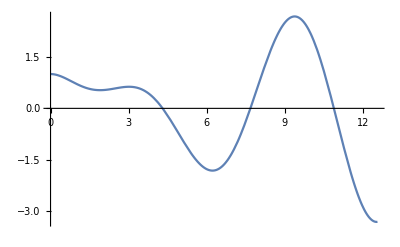

```mathematica
standartEPlot=Plot[Evaluate[y[t]/.stE⟦1, 1⟧], {t, 0, 4π}]
```

```mathematica
euler[h_, a_, b_]:=(
ptr = a;
y0 = 1;
z0 = 0;
yList = {y0};
While[ptr ≤  b,
y1 = y0 + h*z0;
AppendTo[yList, y1];
z1 = z0+h(-0.2z0-y0+Sin[ptr]);
z0 = z1;
y0 = y1;
ptr+=h;
];
yList
);
```

```mathematica
euler[0.01, 0, 4π];
```

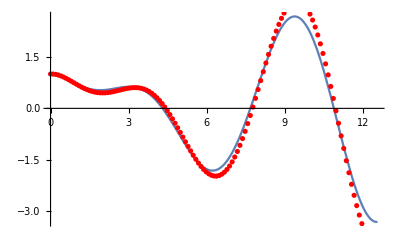

```mathematica
Show[standartEPlot, ListPlot[euler[0.1, 0, 4π],DataRange->{0,4π}, PlotStyle->Red]]
```

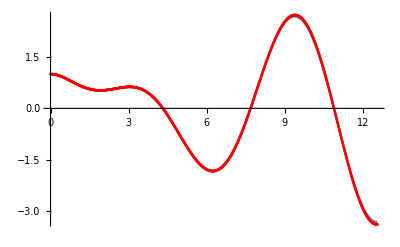

```mathematica
Show[standartEPlot, ListPlot[euler[0.01, 0, 4π],DataRange->{0,4π}, PlotStyle->Red]]
```

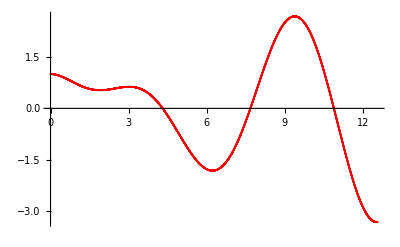

```mathematica
Show[standartEPlot, ListPlot[euler[0.001, 0, 4π],DataRange->{0,4π}, PlotStyle->Red]]
```

```mathematica
absError[h_, a_, b_]:=(
exactValueList=(stE⟦1, 1, 2⟧/.t-> #)&/@Range[a, b, h];
exactValueList - Drop[euler[h, a, b], -1]//Abs
);
```

```mathematica
abs1 =absError[0.001, 0, 4π];
```

```mathematica
abs2 = absError[0.01, 0, 4π];
```

```mathematica
abs3 = absError[0.1, 0, 4π];
```

```mathematica
relError[h_, a_, b_]:=(
exactValueList=(stE⟦1, 1, 2⟧/.t-> #)&/@Range[a, b, h];
result =Abs[(exactValueList - Drop[euler[h, a, b], -1])/exactValueList];
result
);
```

```mathematica
relError[0.001, 0, 4π]
```

{8.88178×10^-16,4.998×10^-7,9.98401×10^-7,1.4958×10^-6,1.99201×10^-6,2.48702×10^-6,2.98082×10^-6,3.47344×10^-6,12551,0.00216446,0.00216534,0.00216622,0.00216711,0.00216799,0.00216887,0.00216975,0.00217063}
 |  |  |  |

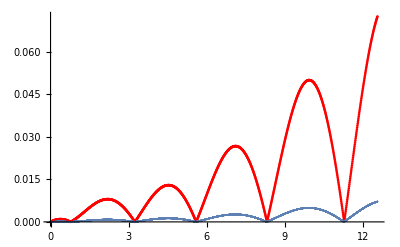

```mathematica
Show[ListPlot[absError[0.01, 0, 4π],DataRange->{0,4π},PlotStyle->Red],ListPlot[absError[0.001, 0, 4π],DataRange->{0,4π}]]
```

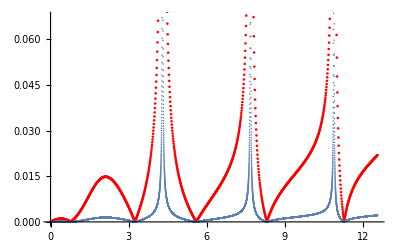

```mathematica
Show[ListPlot[relError[0.01, 0, 4π],DataRange->{0,4π},PlotStyle->Red],ListPlot[relError[0.001, 0, 4π],DataRange->{0,4π}]]
```